```mathematica
(*Solve the Radioactive decay eq by Dsolve command with initial contiditions N(0)=1000 at t=0 *)
```

```mathematica
eq=n'[t]+n[t]/T==0;
Sol=DSolve[eq,n[t],t]
```

{{n[t]→ⅇ^(-t/T) C[1]}}

```mathematica
nt=n[t]/.Sol[[1]]
```

ⅇ^(-t/T) C[1]

```mathematica
nt=nt/.T->1/E
```

ⅇ^(-ⅇ t) C[1]

```mathematica
eq1=(nt/.t->0)==1000
```

C[1]==1000

```mathematica
eq2=nt/.C[1]->1000
```

1000 ⅇ^(-ⅇ t)

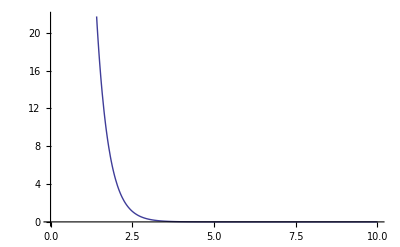

```mathematica
Plot[eq2,{t,0,10}]
```

```mathematica
(*solve the eq of pendulm with initial conditions th=1 at t=0*)
```

```mathematica
eqp=th''[t]+g/l*th[t]==0;
solp=DSolve[eqp,th[t],t]
```

{{th[t]→C[1] Cos[(√g t)/(√l)]+C[2] Sin[(√g t)/(√l)]}}

```mathematica
solp=th[t]/.solp[[1]]
```

C[1] Cos[(√g t)/(√l)]+C[2] Sin[(√g t)/(√l)]

```mathematica
solp=solp/.{g->9.8,l->100}
```

C[1] Cos[0.31305 t]+C[2] Sin[0.31305 t]

0.31305 C[2] Cos[0.31305 t]-0.31305 C[1] Sin[0.31305 t]

```mathematica
eq1=(solp/.t->0)==0
eq2=(solp/.t->1)==1
```

C[1]==0

0.951399 C[1]+0.307961 C[2]==1

```mathematica
constant=Solve[{eq1,eq2},{C[1],C[2]}]
```

{{C[1]→0.,C[2]→3.24716}}

```mathematica
solp=solp/.constant[[1]]
```

0. Cos[0.31305 t]+3.24716 Sin[0.31305 t]

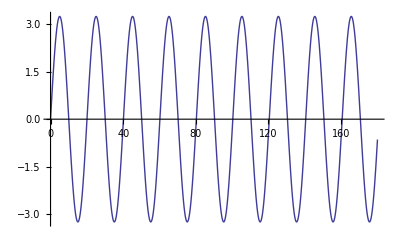

```mathematica
Plot[solp,{t,0,180}]
```

```mathematica
(*alternative method*)
```

```mathematica
eq1=th'[t]-w[t]==0;
eq2=w'[t]+g/l*th[t]==0;
sol=DSolve[{eq1,eq2},{th[t],w[t]},t]
```

{{th[t]→C[1] Cos[(√g t)/(√l)]+(√l C[2] Sin[(√g t)/(√l)])/(√g),w[t]→C[2] Cos[(√g t)/(√l)]-(√g C[1] Sin[(√g t)/(√l)])/(√l)}}

```mathematica
sol1=th[t]/.sol[[1]]
```

C[1] Cos[(√g t)/(√l)]+(√l C[2] Sin[(√g t)/(√l)])/(√g)

```mathematica
sol2=w[t]/.sol[[1]]
```

C[2] Cos[(√g t)/(√l)]-(√g C[1] Sin[(√g t)/(√l)])/(√l)

```mathematica
theta=sol1/.{g->9.8,l->100}
omega=sol2/.{g->9.8,l->100}
```

C[1] Cos[0.31305 t]+3.19438 C[2] Sin[0.31305 t]

C[2] Cos[0.31305 t]-0.31305 C[1] Sin[0.31305 t]

```mathematica
eqq1=(sol1/.t->0)==5
eqq2=(sol2/.t->0)==0
```

C[1]==5

C[2]==0

```mathematica
constant=Solve[{eqq1,eqq2},{C[1],C[2]}]
```

{{C[1]→5,C[2]→0}}

```mathematica
theta=theta/.constant[[1]]
omega=omega/.constant[[1]]
```

5 Cos[0.31305 t]

-1.56525 Sin[0.31305 t]

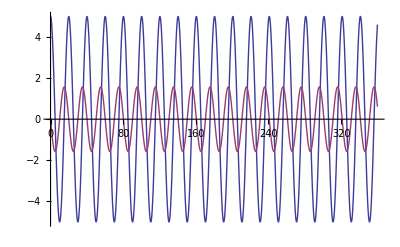

```mathematica
Plot[{theta,omega},{t,0,360}]
```